```mathematica
SetDirectory["C:\\Users\\nanma\\Documents\\GitHub\\hyperbolic_tiling"];
```

```mathematica
maxExplosionFactor=10.0;
frameCount=150;

maxExplosionFactor=8.0;
frameCount=6;

cellThreshold=10;
(*cellThreshold=40;*)

argv=Rest@$ScriptCommandLine;
If[Length[argv]<3,Print["Usage: wolframscript.exe explode_honeycomb.wls <p> <q> <r> <cellThreshold>"];];

If[Length[argv]>=3,p=ToExpression[argv[[1]]];q=ToExpression[argv[[2]]];r=ToExpression[argv[[3]]],p=7;q=3;r=3;];

If[Length[argv]>=4,cellThreshold=ToExpression[argv[[4]]]];

Print["{"<>IntegerString[p]<>", "<>IntegerString[q]<>", "<>IntegerString[r]<>"}"];
shape="explode_"<>ToString[p,InputForm]<>"_"<>ToString[q,InputForm]<>"_"<>ToString[r,InputForm];

dataFolder="data";
imageFolder="images";
epsilon=0.00000001;
imageSize={4,3}/3*720;
lighting={{"Point",White,{10,-10,10}*5}};
rangeFactor=1.25;
colors=Join[{Red,Blue,Green,Yellow,Magenta,LightCyan,Brown,Orange,Pink,Darker[Gray,0.2],Cyan},RandomColor[80]];

outputFolder=FileNameJoin[{imageFolder,"explode_honeycombs"}];
If[!DirectoryQ[outputFolder],CreateDirectory[outputFolder]];
exportToPov=True;
splitEdgeParts=15;

Needs["POVRayRender`"];
ConfigurePOVRayRender["POVRayPath"->"C:\\Program Files\\POV-Ray\\v3.7\\bin\\pvengine64.exe"];

phi=(1+Sqrt[5])/2;
splitEdge[edge_,n_]:=Table[{k edge[[1]]+(1-k) edge[[2]],(k+1/n) edge[[1]]+(1-k-1/n) edge[[2]]},{k,0,1-1/n,1/n}];
splitFaceToTriangles[face_]:=Table[{face[[1]],face[[k-1]],face[[k]]},{k,3,Length[face]}];
HInner[v_,u_]:=2*v[[1]]*u[[1]]-Dot[v,u];
HNormSquare[v_]:=HInner[v,v];
HNorm[v_]:=Sqrt[HNormSquare[v]];
HNormalize[v_,norm_]:=v/HNorm[v]*norm;
Rotation[t_]:={{1,0,0},{0,Cos[t],Sin[t]},{0,-Sin[t],Cos[t]}};

cellCenterToOrigin=ArrayFlatten[{{1,0},{0,RotationMatrix[{-{1,1,1},{1,0,0}}]}}];
Boost[boost_]:={{Cosh[boost],Sinh[boost],0,0},{Sinh[boost],Cosh[boost],0,0},{0,0,1,0},{0,0,0,1}};

HReflect[point_,mirror_]:=point-2*HInner[point,mirror]/HInner[mirror,mirror]*mirror;
centralReflect[point_,mirror_]:=-HReflect[point,mirror];
HDoubleReflect[point_,mirror1_,mirror2_]:=HReflect[HReflect[point,mirror1],mirror2];
ApproxSamePoint[point1_,point2_]:=Round[point1,epsilon]==Round[point2,epsilon];
ApproxSamePointLoose[point1_,point2_]:=Round[point1,10 epsilon]==Round[point2,10 epsilon];

getEdgesFromFace[face_]:=Table[{face[[i+1]],face[[Mod[i+1,Length[face]]+1]]},{i,0,Length[face]-1}];
sameCenter[set1_,set2_]:=ApproxSamePoint[Mean[N[set1]],Mean[N[set2]]];
sameCellCenter[cell1_,cell2_]:=sameCenter[Flatten[cell1,1],Flatten[cell2,1]];
getCellCenter[cell_]:=Total[Flatten[cell,1]]/Length[Flatten[cell,1]];
getCellHeight[cell_]:=getCellCenter[cell][[1]];
opaqueFactor=2/3;
getOpacityByExplosion[factor_]:=If[factor<maxExplosionFactor*opaqueFactor,1,1/(1-opaqueFactor)-1/(1-opaqueFactor)/maxExplosionFactor*factor];

getSplitEdges[edges_]:=Module[{splitEdges,eid,edge,norm,splitParts},splitEdges={};
For[eid=1,eid<=Length[edges],eid++,edge=edges[[eid]];
norm=HNorm[edge[[1]]];
splitParts=splitEdge[edge,splitEdgeParts];
splitParts=Map[HNormalize[#,norm]&,splitParts,{2}];
splitEdges=Join[splitEdges,splitParts];];
splitEdges];

getHyperboloid[v_]:={v[[2]],v[[3]],v[[4]]};
getKlein[v_]:={v[[2]],v[[3]],v[[4]]}/v[[1]];
getPoincare[v_]:={v[[2]],v[[3]],v[[4]]}/(1+v[[1]]);
getPoincareExploded[v_,norm_]:=norm {v[[2]],v[[3]],v[[4]]}/(norm+v[[1]]);
explodedCell[cell_,explosionFactor_]:=Map[(#+Mean[Map[Mean,cell]]*(HNorm[First[First[cell]]]/HNorm[Mean[Map[Mean,cell]]])^1.5*explosionFactor)&,cell,{2}];

explodeCellsByStep[cells_,refCellCenters_,explosionFactor_,explosionStep_,heightsMap_]:=Module[{inactiveCells,activeCells},If[explosionStep==0,inactiveCells={};
activeCells=cells,If[explosionStep==2,inactiveCells=Select[cells,Length[Intersection[{getCellCenter[#]},refCellCenters,SameTest->ApproxSamePoint]]>0&];
activeCells=Select[cells,Length[Intersection[{getCellCenter[#]},refCellCenters,SameTest->ApproxSamePoint]]==0&],(*explosionStep==1*)inactiveCells=Select[cells,Norm[getCellCenter[#][[Range[2,4]]]]<epsilon&];
activeCells=Select[cells,Norm[getCellCenter[#][[Range[2,4]]]]>epsilon&&Length[Intersection[{getCellCenter[#]},refCellCenters,SameTest->ApproxSamePoint]]>0&]
(*inactiveCells={};*)
(*activeCells=Select[cells,Length[Intersection[{getCellCenter[#]},refCellCenters,SameTest->ApproxSamePoint]]>0&];*)];];
For[acId=1,acId<=Length[activeCells],acId++,cell=activeCells[[acId]];
height=getCellHeight[cell];
layer=heightsMap[Round[height,epsilon]];
nonlinearFactor=getNonlinearFactor[explosionFactor,layer];
Print["{acId, nonlinearFactor, layer}"];
Print[{acId,nonlinearFactor,layer}];
activeCells[[acId]]=explodedCell[cell,nonlinearFactor];];
(*activeCells=Map[explodedCell[#,explosionFactor]&,activeCells];*){activeCells,inactiveCells}];


filterCells[cells_,cellThreshold_]:=Module[{cellCenterHeights,heightTally,tallyCounts,includeCount,heightThreshold,levelIndex},cellCenterHeights=Map[getCellHeight,cells];
heightTally=Tally[cellCenterHeights,ApproxSamePoint]//Sort;
tallyCounts=Map[#[[2]]&,heightTally];
Print[tallyCounts];
includeCount=0;
heightThreshold=-1;
For[levelIndex=1,levelIndex<=Length[heightTally],levelIndex++,If[includeCount<cellThreshold,includeCount+=heightTally[[levelIndex]][[2]];
If[includeCount>=cellThreshold,heightThreshold=heightTally[[levelIndex]][[1]]+epsilon];];];
If[heightThreshold==-1,heightThreshold=heightTally[[Length[heightTally]]][[1]]+epsilon];
filteredCells=Select[cells,getCellCenter[#][[1]]<=heightThreshold&];
Print["Filter from "<>IntegerString[Length[cells]]<>" cells down to "<>IntegerString[Length[filteredCells]]<>" cells."];
filteredCells];

getNonlinearFactor[linear_,layer_]:=Module[{layerOffset,linearOffset,returnValue},layerOffset=If[layer>1,layer-1,0];
linearOffset=linear+layerOffset*delayFactor;
returnValue=linearOffset^2/maxExplosionFactor;
(*If[returnValue>maxExplosionFactor,returnValue=maxExplosionFactor];*)If[linearOffset<0,returnValue=0];
returnValue];

dataFileName=FileNameJoin[{dataFolder,"hyper_"<>ToString[p,InputForm]<>"_"<>ToString[q,InputForm]<>"_"<>ToString[r,InputForm]<>"_"<>IntegerString[cellThreshold]<>".wl"}];

If[FileExistsQ[dataFileName],Print["Reading from from "<>dataFileName];
data=Get[dataFileName],(*file do not exist*)Print["data file "<>dataFileName<>" does not exist"];
Print["cell threshold can only be 100, 300, or 1000"];
Exit[];];

cells=data["cells"];
Print[cells//Length];

(*353:{1,20,60,12,120} 1,21,81,93,213 535:{1,12,60,120} 1,13,73,193*)

newCellThreshold=cellThreshold;
layers=1;

If[{p,q,r}=={6,3,3}&&cellThreshold==10&&False,(*1+20+60+12*)newCellThreshold=4;
layers=1;];

(*for testing,1+20*)
(*newCellThreshold=21;*)

cellCenterHeights=Map[getCellCenter[#][[1]]&,cells];
heightTally=Tally[cellCenterHeights,ApproxSamePoint]//Sort;
tallyCounts=Map[#[[2]]&,heightTally];
Print["heights"];
Print[heightTally];
Print[tallyCounts];
layers=Length[tallyCounts];
Print["Setting layers to: "<>IntegerString[layers]];

delayFactor=If[layers>=4,2,3];

cellCenters=Map[getCellCenter,cells];
cellCenters=Sort[cellCenters];
Map[Print,cellCenters];
Map[Print[HNorm[#]]&,cellCenters];
(*Exit[];*)
```

Rest::norest: Cannot take Rest of expression {} with length zero.

Usage: wolframscript.exe explode_honeycomb.wls <p> <q> <r> <cellThreshold>

{7, 3, 3}

data file data\hyper_7_3_3_10.wl does not exist

cell threshold can only be 100, 300, or 1000

```mathematica
getNonCompactCellCenter[cell_]:=Module[
{samplePoints,face1Points,face2id,centerSolution},
face1Points=cell[[1]][[Range[3]]];
For[face2id=1,face2id<=Length[cell[[2]]],face2id++,
samplePoints=Join[face1Points,{cell[[2]][[face2id]]}];
If[Abs[Det[samplePoints]]>epsilon,Break[]];
];
If[Abs[Det[samplePoints]]<=epsilon,
Print["Cannot construct samplePoints"];
Return[]];
centerSolution=Solve[HInner[{w,x,y,z},samplePoints[[1]]]==HInner[{w,x,y,z},samplePoints[[2]]]&&HInner[{w,x,y,z},samplePoints[[1]]]==HInner[{w,x,y,z},samplePoints[[3]]]&&HInner[{w,x,y,z},samplePoints[[1]]]==HInner[{w,x,y,z},samplePoints[[4]]]&&w==1,{w,x,y,z}];
{w,x,y,z}/.centerSolution[[1]]
];
centers=Table[getNonCompactCellCenter[cells[[i]]],{i,Length[cells]}]
```

{{1.,-0.732238,-0.732238,-0.732238},{1.,-0.732238,0.732238,0.732238},{1.,0.732238,-0.732238,0.732238},{1.,0.732238,0.732238,-0.732238},{1.,-0.600277,-0.600277,0.600277},{1.,-0.600277,0.600277,-0.600277},{1.,0.600277,-0.600277,-0.600277},{1.,0.600277,0.600277,0.600277},{1.,-0.938565,-0.268625,0.268625},{1.,-0.938565,0.268625,-0.268625},{1.,-0.268625,-0.938565,0.268625},{1.,-0.268625,-0.268625,0.938565},{1.,-0.268625,0.268625,-0.938565},{1.,-0.268625,0.938565,-0.268625},{1.,0.268625,-0.938565,-0.268625},{1.,0.268625,0.268625,0.938565},{1.,0.268625,-0.268625,-0.938565},{1.,0.268625,0.938565,0.268625},{1.,0.938565,-0.268625,-0.268625},{1.,0.938565,0.268625,0.268625}}

{439.,424.777,410.908,397.388,384.208,371.36,358.838,346.635,334.743,323.156,311.867,300.869,290.156,279.721,269.559,259.663,250.027,240.646,231.513,222.623,213.97,205.549,197.355,189.382,181.625,174.079,166.739,159.601,152.659,145.909,139.347,132.967,126.766,120.739,114.882,109.19,103.661,98.2891,93.0714,88.0039,83.0828,78.3045,73.6655,69.1622,64.7912,60.5492,56.4329,52.4391,48.5647,44.8065,41.1616,37.6271,34.2,30.8776,27.6571,24.5358,21.5111,18.5803,15.7411,12.9909,10.3274,7.74808,5.25078,2.83322,0.493208,-1.7714,-3.9627,-6.08272,-8.13348,-10.1169,-12.0349,-13.8894,-15.6821,-17.4148,-19.0893,-20.7072,-22.2702,-23.7799,-25.2378,-26.6455,-28.0045,-29.3163,-30.5821,-31.8035,-32.9818,-34.1182,-35.2141,-36.2707,-37.2893,-38.2709,-39.2168,-40.128,-41.0058,-41.851,-42.6649,-43.4483,-44.2022,-44.9277,-45.6256,-46.2968,-46.9423,-47.5628,-48.1592,-48.7324,-49.283,-49.8118,-50.3197,-50.8073,-51.2753,-51.7244,-52.1552,-52.5684,-52.9646,-53.3445,-53.7085,-54.0573,-54.3914,-54.7113,-55.0177,-55.3108,-55.5914,-55.8597,-56.1163,-56.3617,-56.5962,-56.8202,-57.0343,-57.2386,-57.4337,-57.6199,-57.7975,-57.9669,-58.1284,-58.2823,-58.429,-58.5687,-58.7017,-58.8283,-58.9487,-59.0633,-59.1722,-59.2757,-59.3741,-59.4675,-59.5562,-59.6403,-59.7202,-59.7959,-59.8676,-59.9356,-60.}

{{385.442,360.87,337.692,315.834,295.231,275.817,257.53,240.312,224.106,208.859,194.521,181.044,168.381,156.488,145.324,134.85,125.027,115.821,107.196,99.1219,91.5665,84.501,77.898,71.731,65.9753,60.6071,55.6041,50.945,46.6097,42.5791,38.835,35.3605,32.1391,29.1557,26.3955,23.845,21.4911,19.3215,17.3246,15.4894,13.8055,12.2632,10.8532,9.56681,8.3958,7.33241,6.36935,5.49972,4.71705,4.01524,3.38856,2.83159,2.33928,1.90685,1.52983,1.20401,0.925451,0.690458,0.495565,0.337528,0.213309,0.120066,0.0551414,0.0160543,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004},{439.922,413.643,388.801,365.321,343.136,322.18,302.391,283.708,266.075,249.438,233.745,218.948,204.999,191.854,179.471,167.809,156.831,146.498,136.778,127.637,119.043,110.967,103.381,96.2569,89.5703,83.2966,77.4129,71.8972,66.7288,61.8882,57.3567,53.1165,49.151,45.4443,41.9813,38.7478,35.7304,32.9162,30.2931,27.8498,25.5754,23.4597,21.4931,19.6663,17.9707,16.3983,14.9413,13.5924,12.3448,11.192,10.128,9.14684,8.24328,7.41216,6.64868,5.9483,5.30678,4.7201,4.1845,3.69644,3.25259,2.84984,2.48524,2.15604,1.85967,1.59371,1.35588,1.14407,0.95629,0.790675,0.645488,0.519105,0.410006,0.316775,0.238088,0.172713,0.1195,0.0773799,0.0453568,0.0225048,0.00796371,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004},{498.002,470.017,443.51,418.408,394.641,372.143,350.851,330.704,311.644,293.617,276.569,260.452,245.218,230.821,217.218,204.369,192.234,180.776,169.96,159.751,150.119,141.033,132.463,124.383,116.765,109.586,102.822,96.4493,90.448,84.7973,79.4783,74.4725,69.7629,65.3329,61.1671,57.2507,53.5697,50.1109,46.8617,43.8103,40.9454,38.2563,35.7329,33.3657,31.1457,29.0642,27.1132,25.2851,23.5726,21.9688,20.4673,19.0621,17.7473,16.5175,15.3675,14.2926,13.2881,12.3497,11.4734,10.6554,9.89188,9.17961,8.51533,7.89603,7.31886,6.78114,6.28036,5.81415,5.38027,4.97665,4.6013,4.25238,3.92816,3.627,3.34737,3.08785,2.84708,2.62379,2.41682,2.22504,2.04742,1.88298,1.73082,1.59008,1.45997,1.33973,1.22868,1.12616,1.03155,0.944308,0.863884,0.789789,0.721561,0.65877,0.601014,0.54792,0.499139,0.454349,0.413248,0.375554,0.341008,0.309368,0.280408,0.25392,0.229709,0.207597,0.187416,0.169012,0.152242,0.136973,0.123082,0.110457,0.0989931,0.0885925,0.0791662,0.0706318,0.062913,0.0559398,0.0496475,0.0439765,0.0388721,0.0342839,0.0301656,0.0264746,0.023172,0.0202218,0.0175913,0.0152505,0.0131717,0.0113299,0.00970202,0.00826703,0.00700578,0.0059008,0.00493617,0.00409739,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004}}

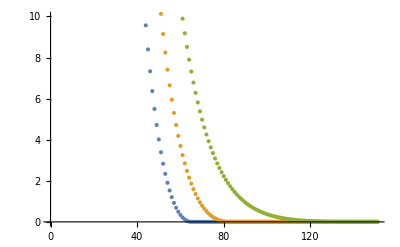

```mathematica
maxExplosionFactor=500;
layers=3;
delayFactor=30;
frameCount=150;
kExponent=8;
getNonlinearFactor[linear_,layer_]:=Module[{layerOffset,linearOffset,returnValue},minFactor=0.004;
layerOffset=If[layer>1,layer-1,0];
linearOffset=linear+layerOffset*delayFactor;
returnValue=linearOffset^2/maxExplosionFactor;
(*If[returnValue>maxExplosionFactor,returnValue=maxExplosionFactor];*)If[linearOffset<0||returnValue<minFactor,returnValue=minFactor];
returnValue];
maxk=maxExplosionFactor^(1/kExponent);
explosionFactors=Table[(k^kExponent-1.)+(-layers+1)*delayFactor,{k,maxk,1,-(maxk-1)/frameCount}];
explosionFactors
Table[getNonlinearFactor[explosionFactors[[fid]],layer ],{layer,layers},{fid,Length[explosionFactors]}]
ListPlot[Table[getNonlinearFactor[explosionFactors[[fid]],layer ],{layer,layers},{fid,Length[explosionFactors]}],PlotRange->{0,10}]
```

{10.,9.89262,9.78523,9.67785,9.57047,9.46309,9.3557,9.24832,9.14094,9.03356,8.92617,8.81879,8.71141,8.60403,8.49664,8.38926,8.28188,8.1745,8.06711,7.95973,7.85235,7.74497,7.63758,7.5302,7.42282,7.31544,7.20805,7.10067,6.99329,6.88591,6.77852,6.67114,6.56376,6.45638,6.34899,6.24161,6.13423,6.02685,5.91946,5.81208,5.7047,5.59732,5.48993,5.38255,5.27517,5.16779,5.0604,4.95302,4.84564,4.73826,4.63087,4.52349,4.41611,4.30872,4.20134,4.09396,3.98658,3.87919,3.77181,3.66443,3.55705,3.44966,3.34228,3.2349,3.12752,3.02013,2.91275,2.80537,2.69799,2.5906,2.48322,2.37584,2.26846,2.16107,2.05369,1.94631,1.83893,1.73154,1.62416,1.51678,1.4094,1.30201,1.19463,1.08725,0.979866,0.872483,0.765101,0.657718,0.550336,0.442953,0.33557,0.228188,0.120805,0.0134228,-0.0939597,-0.201342,-0.308725,-0.416107,-0.52349,-0.630872,-0.738255,-0.845638,-0.95302,-1.0604,-1.16779,-1.27517,-1.38255,-1.48993,-1.59732,-1.7047,-1.81208,-1.91946,-2.02685,-2.13423,-2.24161,-2.34899,-2.45638,-2.56376,-2.67114,-2.77852,-2.88591,-2.99329,-3.10067,-3.20805,-3.31544,-3.42282,-3.5302,-3.63758,-3.74497,-3.85235,-3.95973,-4.06711,-4.1745,-4.28188,-4.38926,-4.49664,-4.60403,-4.71141,-4.81879,-4.92617,-5.03356,-5.14094,-5.24832,-5.3557,-5.46309,-5.57047,-5.67785,-5.78523,-5.89262,-6.}

{{1598.27,1345.21,1130.17,947.768,793.327,662.807,552.712,460.027,382.156,316.863,262.233,216.621,178.622,147.037,120.843,99.1724,81.2866,66.5616,54.4697,44.5659,36.4762,29.8865,24.534,20.199,16.6986,13.8809,11.6199,9.81167,8.3703,7.2254,6.31923,5.60468,5.04336,4.60416,4.26191,3.99633,3.79114,3.63332,3.504,3.37803,3.25436,3.13299,3.01394,2.89718,2.78274,2.6706,2.56077,2.45324,2.34802,2.24511,2.1445,2.0462,1.9502,1.85651,1.76513,1.67605,1.58928,1.50482,1.42266,1.3428,1.26526,1.19002,1.11708,1.04646,0.978136,0.912121,0.848412,0.78701,0.727913,0.671123,0.616639,0.564461,0.514589,0.467024,0.421765,0.378812,0.338165,0.299824,0.26379,0.230062,0.19864,0.169524,0.142714,0.118211,0.0960137,0.0761227,0.0585379,0.0432593,0.0302869,0.0196207,0.0112608,0.00520697,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004},{106145.,92953.3,81310.9,71046.5,62006.7,54054.,47065.4,40930.9,35552.3,30841.9,26721.6,23121.8,19980.6,17242.9,14860.1,12788.8,10990.6,9431.59,8081.87,6914.95,5907.51,5039.01,4291.4,3648.84,3097.4,2624.92,2220.73,1875.54,1581.22,1330.72,1117.87,937.341,784.508,655.361,546.438,454.751,377.728,313.155,259.133,214.036,176.471,145.251,119.365,97.9506,80.2797,65.7337,53.7908,44.0107,36.0234,29.5182,24.2353,19.9575,16.5039,13.7245,11.4946,9.71163,8.29072,7.16231,6.2694,5.56546,5.01262,4.58017,4.24325,3.98189,3.78001,3.62478,3.49606,3.37023,3.24671,3.12549,3.00657,2.88996,2.77566,2.66367,2.55398,2.4466,2.34152,2.23875,2.13829,2.04013,1.94428,1.85073,1.75949,1.67056,1.58393,1.49961,1.4176,1.33789,1.26049,1.18539,1.1126,1.04212,0.973943,0.908072,0.844507,0.783249,0.724296,0.66765,0.61331,0.561277,0.511549,0.464128,0.419013,0.376204,0.335701,0.297505,0.261614,0.22803,0.196752,0.167781,0.141115,0.116756,0.0947029,0.0749561,0.0575154,0.042381,0.0295527,0.0190307,0.0108148,0.00490518,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004},{2.94247×10^6,2.64192×10^6,2.37034×10^6,2.12509×10^6,1.9038×10^6,1.70425×10^6,1.52444×10^6,1.36253×10^6,1.21686×10^6,1.08588×10^6,968211.,862579.,767826.,682899.,606840.,538780.,477926.,423563.,375039.,331764.,293205.,258879.,228348.,201218.,177133.,155771.,136843.,120088.,105272.,92182.1,80630.7,70447.2,61479.2,53590.2,46658.1,40573.6,35239.2,30567.9,26482.,22912.6,19798.2,17084.1,14721.9,12668.8,10886.5,9341.4,8003.84,6847.54,5849.35,4988.92,4248.32,3611.84,3065.68,2597.76,2197.52,1855.73,1564.35,1316.37,1105.69,927.023,775.781,647.994,540.231,449.532,373.349,309.488,256.069,211.481,174.345,143.487,117.903,96.7435,79.2849,64.916,53.1203,43.4625,35.5763,29.1547,23.9405,19.7192,16.3119,13.5702,11.3711,9.61301,8.21227,7.10013,6.2203,5.52683,4.98235,4.55654,4.22489,3.96767,3.76906,3.61638,3.48813,3.36244,3.23906,3.11799,2.99922,2.88275,2.7686,2.65675,2.5472,2.43996,2.33503,2.2324,2.13208,2.03407,1.93836,1.84496,1.75387,1.66508,1.5786,1.49442,1.41255,1.33299,1.25573,1.18078,1.10813,1.03779,0.969758,0.904031,0.840611,0.779496,0.720688,0.664186,0.609991,0.558101,0.508518,0.46124,0.41627,0.373605,0.333246,0.295194,0.259448,0.226008,0.194874,0.166047,0.139525,0.11531,0.0934012,0.0737985,0.056502,0.0415116,0.0288275,0.0184496,0.0103779,0.0046124,0.004,0.004}}

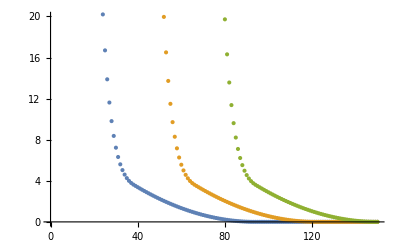

```mathematica
maxExplosionFactor=10;
layers=3;
delayFactor=3;
frameCount=150;
transitionFraction=0.6;
newExponent=2*8;
new[x_]:=x^newExponent/maxExplosionFactor^(newExponent-1)/transitionFraction^(newExponent-2)/(newExponent/2)+maxExplosionFactor transitionFraction^2/(newExponent/2)*(newExponent/2-1);
getNonlinearFactor[linear_,layer_]:=Module[{layerOffset,linearOffset,returnValue},minFactor=0.004;
layerOffset=If[layer>1,layer-1,0];
linearOffset=linear+layerOffset*delayFactor;
returnValue=If[linearOffset > transitionFraction maxExplosionFactor, new[linearOffset],linearOffset^2/maxExplosionFactor];
(*If[returnValue>maxExplosionFactor,returnValue=maxExplosionFactor];*)If[linearOffset<0||returnValue<minFactor,returnValue=minFactor];
returnValue];
explosionFactors=Table[k*1.0,{k,maxExplosionFactor,(-layers+1)*delayFactor,-(maxExplosionFactor+(layers-1)*delayFactor)/(frameCount-1)}];
explosionFactors
Table[getNonlinearFactor[explosionFactors[[fid]],layer ],{layer,layers},{fid,Length[explosionFactors]}]
ListPlot[Table[getNonlinearFactor[explosionFactors[[fid]],layer ],{layer,layers},{fid,Length[explosionFactors]}],PlotRange->{0,20}]
```

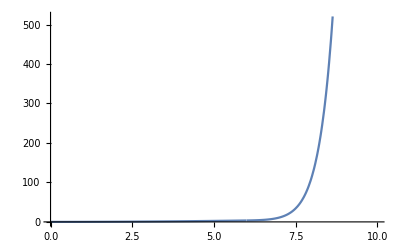

```mathematica
t=0.6;
m=10;
newExponent=2*10;
new[x_]=x^newExponent/m^(newExponent-1)/t^(newExponent-2)/(newExponent/2)+m t^2/(newExponent/2)*(newExponent/2-1);
Plot[If[x>t m,new[x],x^2/m],{x,0,m}]
```

```mathematica
Clear[t];
Clear[m];
x^2/m/.x->t m
D[x^2/m,x]/.x->t m
```

m t^2

2 t

```mathematica
Clear[t];
Clear[m];
newExponent=2*4;
new[x_]=x^newExponent/m^(newExponent-1)/t^(newExponent-2)/(newExponent/2)+m t^2/(newExponent/2)*(newExponent/2-1);
new[x]/.x->t m
D[new[x],x]/.x->t m
```

m t^2

2 t